```mathematica
ClearAll[P,F,M]
```

```mathematica
P[t_]:= {F[t], M[t]}
```

```mathematica
ODE={{(1-Subscript[μ, FM]),α*Subscript[μ, MF]},{Subscript[μ, FM],α*(1-Subscript[μ, MF])}}
```

{{1-μ_FM,α μ_MF},{μ_FM,α (1-μ_MF)}}

```mathematica
MatrixForm[ODE]
```

(1-μ_FM | α μ_MF
μ_FM | α (1-μ_MF))

```mathematica
Eigenvalues[ODE]
```

{1/2 (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)),1/2 (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))}

```mathematica
DSolve[{P'[t]==ODE.P[t], P[0]=={1,0}},P[t],t]
```

{{F[t]→1/(2 √(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))(-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) μ_FM-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) μ_FM-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α μ_MF+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α μ_MF+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) √(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) √(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)),M[t]→-((ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))) μ_FM)/(√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))}}

```mathematica
FullSimplify[DSolve[{P'[t]==ODE.P[t], P[0]=={1,0}},P[t],t]]
```

{{F[t]→1/(2 √(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF)))ⅇ^(-1/2 t (-1+μ_FM+α (-1+μ_MF)+√(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF)))) (-1+α+μ_FM-α μ_MF-ⅇ^(t √(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF))) (-1+α+μ_FM-α μ_MF)+√(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF))+ⅇ^(t √(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF))) √(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF))),M[t]→(2 ⅇ^(-1/2 t (-1-α+μ_FM+α μ_MF)) Sinh[1/2 t √(4 α (-1+μ_FM+μ_MF)+(-1-α+μ_FM+α μ_MF)^2)] μ_FM)/(√(4 α (-1+μ_FM+μ_MF)+(-1-α+μ_FM+α μ_MF)^2))}}

```mathematica
Eigenvalues[ODE]
```

{1/2 (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)),1/2 (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))}

```mathematica
FullSimplify[Eigenvectors[ODE]]
```

{{-(-1+α+μ_FM-α μ_MF+√(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF)))/(2 μ_FM),1},{(1-μ_FM+α (-1+μ_MF)+√(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF)))/(2 μ_FM),1}}

```mathematica
Expand[(1-α+α Subscript[μ, MF])^2-4 (α-α Subscript[μ, FM]-α Subscript[μ, MF])]
```

1-6 α+α^2+4 α μ_FM+6 α μ_MF-2 α^2 μ_MF+α^2 μ_MF^2

```mathematica
FullSimplify[Eigenvalues[ODE]]
```

{1/2 (1+α-μ_FM-α μ_MF-√(4 α (-1+μ_FM+μ_MF)+(-1-α+μ_FM+α μ_MF)^2)),1/2 (1+α-μ_FM-α μ_MF+√(4 α (-1+μ_FM+μ_MF)+(-1-α+μ_FM+α μ_MF)^2))}

```mathematica
DSolve[{P'[t]==ODE.P[t], P[0]=={1,0}},P[t],t]
```

{{F[t]→1/(2 √(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))(-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) μ_FM-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) μ_FM-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α μ_MF+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α μ_MF+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) √(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) √(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)),M[t]→-((ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))) μ_FM)/(√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))}}

```mathematica
FullSimplify[4 α (-1+Subscript[μ, FM]+Subscript[μ, MF])+(-1-α+Subscript[μ, FM]+α Subscript[μ, MF])^2-Subscript[μ, FM]^2+(1-α+α Subscript[μ, MF])^2+2 Subscript[μ, FM] (-1+α+α Subscript[μ, MF])]
```

2 ((1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF))

```mathematica
FullSimplify[-(-1+α+Subscript[μ, FM]-α Subscript[μ, MF]+√(Subscript[μ, FM]^2+(1-α+α Subscript[μ, MF])^2+2 Subscript[μ, FM] (-1+α+α Subscript[μ, MF])))/(2 Subscript[μ, FM])]
```

-(-1+α+μ_FM-α μ_MF+√(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF)))/(2 μ_FM)

```mathematica
FullSimplify[-(-1+a+b-a*c)+Sqrt[b^2+(1-a-a*c)^2+2*b*(-1+a+a*c)]]
```

1-b+a (-1+c)+√((-1+a+b+a c)^2)

```mathematica
sol =DSolve[{F'[t]== (1-Subscript[μ, FM])F[t] + α*Subscript[μ, MF] M[t], M'[t]== Subscript[μ, FM] F[t] + α(1-Subscript[μ, MF])M[t], F[0]==1, M[0]==0}, {F[t], M[t]}, t]
```

{{F[t]→1/(2 √(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))(-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) μ_FM-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) μ_FM-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α μ_MF+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) α μ_MF+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) √(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)+ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))) √(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)),M[t]→-((ⅇ^(1/2 t (1+α-μ_FM-α μ_MF-√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))-ⅇ^(1/2 t (1+α-μ_FM-α μ_MF+√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2)))) μ_FM)/(√(-4 (α-α μ_FM-α μ_MF)+(-1-α+μ_FM+α μ_MF)^2))}}

```mathematica
FullSimplify[sol]
```

{{F[t]→1/(2 √(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF)))ⅇ^(-1/2 t (-1+μ_FM+α (-1+μ_MF)+√(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF)))) (-1+α+μ_FM-α μ_MF-ⅇ^(t √(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF))) (-1+α+μ_FM-α μ_MF)+√(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF))+ⅇ^(t √(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF))) √(μ_FM^2+(1-α+α μ_MF)^2+2 μ_FM (-1+α+α μ_MF))),M[t]→(2 ⅇ^(-1/2 t (-1-α+μ_FM+α μ_MF)) Sinh[1/2 t √(4 α (-1+μ_FM+μ_MF)+(-1-α+μ_FM+α μ_MF)^2)] μ_FM)/(√(4 α (-1+μ_FM+μ_MF)+(-1-α+μ_FM+α μ_MF)^2))}}

```mathematica
sol = sol/.{α->1.3, Subscript[μ, FM]->0.0039*^-06, Subscript[μ, MF]-> 1.26610510*^-03}
```

{{F[t]→1.67586 (0.596708 ⅇ^(1. t)+4.30271×10^-11 ⅇ^(1.29835 t)),M[t]→-1.30717×10^-8 (ⅇ^(1. t)-ⅇ^(1.29835 t))}}

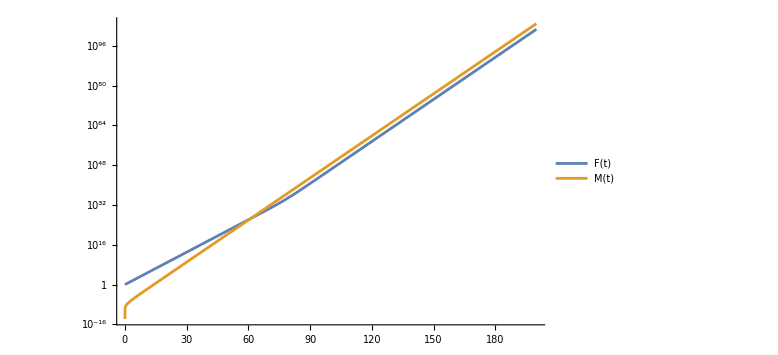

```mathematica
LogPlot[{F[t]/.sol, M[t]/.sol}, {t,0, 200}, ImageSize->Large, PlotLegends->{"F(t)", "M(t)"}]
```

```mathematica
Reduce[{-α(1-2 Subscript[μ, MF])+(1-Subscript[μ, FM]) < 0, 0< α<2, 0<Subscript[μ, FM]<1,0<Subscript[μ, MF]<1},{α,Subscript[μ, MF]}]
```

0<μ_FM<1&&1-μ_FM<α<2&&0<μ_MF<(-1+α+μ_FM)/(2 α)

```mathematica
μFM=0.0039*^-06
f[α_, μMF_]:= ((1 - μFM) + α(1 - μMF) + Sqrt[((1 - μFM) + α(1 - μMF))^2 - 4 * α * (1 - μFM - μMF)]) / ((1 - μFM) + α(1 - μMF) + Sqrt[((1 - μFM) + α(1 - μMF))^2 - 4 * α * (1 - μFM - μMF)] + 2 * μFM)
c[α_, μMF_]:= 2 * μFM/ ((1 -μMF) + α(1 - μMF) + Sqrt[((1 - μFM) + α(1 - μMF))^2 - 4 * α * (1 - μFM - μMF)] + 2 * μFM)
```

3.9×10^-9

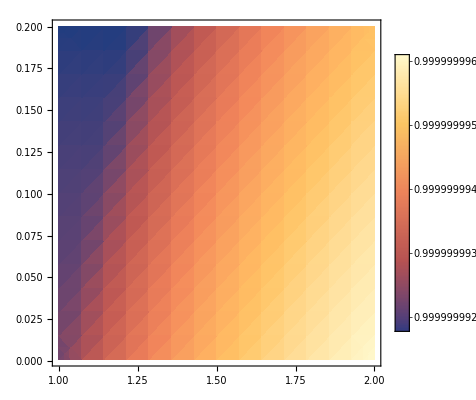

```mathematica
DensityPlot[f[α,μMF]-c[α,μMF], {α, 1, 2}, {μMF, 1*^-3, 2*^-1}, PlotLegends->Automatic]
```

```mathematica
a[α_,μMF_]:=(1-μFM) + α(1 - μMF)
Δ[α_, μMF_]:= a[α, μMF]^2 - 4 * α (1 - μFM - μMF)
```

```mathematica
T[α_, μMF_, t_]:= (a[α, μMF] + 2μMF)Sinh[0.5*Sqrt[Δ[α, μMF]]t] + Sqrt[Δ[α, μMF]]Cosh[0.5Sqrt[Δ[α, μMF]]t]
f[α_, μMF_, t_]:= a[α, μMF]Sinh[0.5*Sqrt[Δ[α, μMF]]t] + Sqrt[Δ[α, μMF]]Cosh[0.5Sqrt[Δ[α, μMF]]t] / T[α, μMF, t]
m[α_, μMF_, t_]:= 2μFM*Sinh[0.5*Sqrt[Δ[α, μMF]]t] + Sqrt[Δ[α, μMF]]Cosh[0.5Sqrt[Δ[α, μMF]]t] / T[α, μMF, t]
```

```mathematica
Plot[{f[1.3, 1.26610510*^-3, t], m[1.3, 1.26610510*^-3, t]},{t, 0 ,400}]
```

-Graphics-